# Electrochemical PCET rate constant with Error-functions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/CHASE/Jerry-Meyer-Reorganization-energy/Mathematica

## Constants and Conversion Factors

## Accuracy settings

```mathematica
AccN=70;
$MaxExtraPrecision=100;
```

## Unit conversions

```mathematica
bohr2a=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"],AccN];
a2bohr=1/bohr2a;
au2kcal=SetAccuracy[QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]],AccN];
kcal2au=1/au2kcal;
ev2kcal=SetAccuracy[QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]],AccN];
kcal2ev=1/ev2kcal;
ev2cm=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"],AccN];
cm2ev=1/ev2cm;
au2ev=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"],AccN];
ev2au=1/au2ev;
au2cm=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"],AccN];
cm2au=1/au2cm;
au2ps=SetAccuracy[QuantityMagnitude@UnitConvert[1/(2π)Entity["PhysicalConstant","PlanckConstant"]["Value"],"Hartrees*ps"],AccN];
ps2au=1/au2ps;
au2s=au2ps*10^-12;
s2au=1/au2s;
```

## Universal constants

```mathematica
hbarau=1; (* in atomic units *)
hbaraups=hbarau au2ps; (* in Hartree × ps *)
hbarkcalps=hbaraups au2kcal; (* in kcal/mol × ps *)
Dalton=SetAccuracy[QuantityMagnitude@UnitConvert[1 Quantity[, "Daltons"],"electronmass"],AccN];
μH=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[, "ProtonMass"],"electronmass"],AccN];
μD=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[, "DeuteronMass"],"electronmass"],AccN];
MassH=μH/Dalton;
MassD=μD/Dalton;
kb=SetAccuracy[QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"],AccN];
```

## Experimental data and calculated reorganization energies

```mathematica
knETdata=ReadList["data/kn-ET-low-pH.csv",{Real,Real}];
knPCETdata=ReadList["data/kn-PCET-high-pH.csv",{Real,Real}];
```

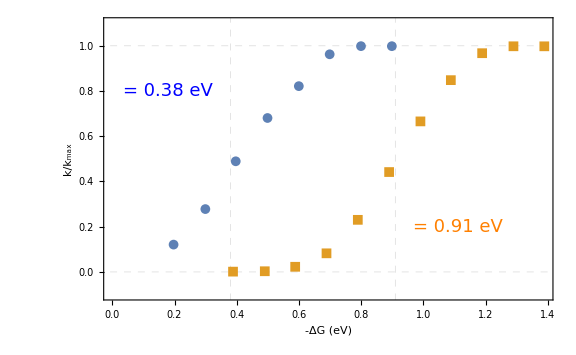

```mathematica
ListPlot[{knETdata,knPCETdata},
PlotRange->{-0.1,1.1},
GridLines->{{0.38,0.91},{0,1}},
GridLinesStyle->Directive[Thickness[Medium],Dashed],
Mesh->All,
PlotMarkers->{Automatic,Medium},
Axes->False,Frame->True,
FrameStyle->Directive[Black,Thickness[Medium]],
ImageSize->Large,
FrameLabel->{"-ΔG (eV)","k/k_max"},
LabelStyle->{18},
Epilog->{
Text[Style[" = 0.38 eV",18,Blue,FontFamily->"Times",Background->White],{0.38-0.2,0.8}],
Text[Style[" = 0.91 eV",18,Orange,FontFamily->"Times",Background->White],{0.91+0.2,0.2}]
}
]
```

```mathematica
VET=0.74 cm2au
ρF=0.45
```

3.37169×10^-6

0.45

Observed (from measured normalized kinetics) reorganization energies:

```mathematica
λETobs=0.38 ev2kcal;
λPCETobs=0.91 ev2kcal;
```

Calculated (from electrostatic model with cylindrical cavity plus innersphere contribution) total reorganization energies:

```mathematica
λETouter=4.87;
λETinner=3.76;
λPCETouter=4.87;
λPCETinner=12.39;
```

```mathematica
λETcalc=λETouter+λETinner
λPCETcalc=λPCETouter+λPCETinner
```

8.63

17.26

## Basic Qualitative Model for PCET

## Marcus-Gerischer PCET model

```mathematica
V^2/ℏ √(π/(λ kT))Subscript[P, μ] Subscript[S, μν]^2 Subscript[ρ, F] Integrate[Exp[-(-x+η+Subscript[Δϵ, μν]+λ)^2/(4λ kT)],{x,-∞,0},Assumptions->{λ>0,kT>0,η∈Reals,Subscript[Δϵ, μν]∈Reals}]
FullSimplify[%,Assumptions->{λ>0,kT>0,η<0,δ∈Reals}]//TraditionalForm
```

(π V^2 √(1/(kT λ)) √(kT λ) Erfc[(η+λ+Δϵ_μν)/(2 √(kT λ))] P_μ S_μν^2 ρ_F)/ℏ

(π V^2 ρ_F P_μ S_μν^2 erfc((Δϵ_μν+η+λ)/(2 √(λ kT))))/ℏ

```mathematica
knETtmp[η_]:=1/2 Erfc[(-η*23.06+15)/(2 √(0.6 15))];
```

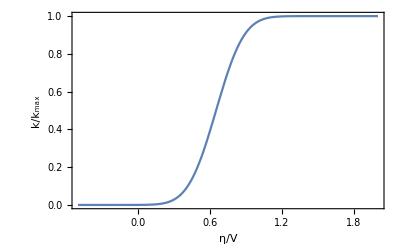

```mathematica
Plot[knETtmp[η],{η,-0.5,2},
Axes->False,Frame->True,
FrameLabel->{"η/V","k/k_max"}]
```

```mathematica
Manipulate[
Plot[{If[nS==0,1/2 Erfc[(-η×ev2kcal+λETobs)/(2 √(kb 300 au2kcal λETobs))],1/(2nS)Sum[Erfc[(n δ-η×ev2kcal+λETobs)/(2 √(kb 300 au2kcal λETobs))],{n,1,nS}]],
1/2 Erfc[(-η×ev2kcal+λeff×ev2kcal)/(2 √(kb 300 au2kcal λeff×ev2kcal))],1/2 Erfc[(-η×ev2kcal+λETobs)/(2 √(kb 300 au2kcal λETobs))]},{η,-0.5,2},
PlotRange->All,ImageSize->Large,
PlotStyle->{Red,{Red,Dashed},Black},
BaseStyle->{FontSize->18},
Axes->False,Frame->True,
FrameLabel->{"η [kcal/mol]","k/k_max"},
GridLines->{{{λETobs/23.06,Black},{λeff,Red}},None},
GridLinesStyle->Directive[Thick,Dashed],
Epilog->{
Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λETobs/23.06-0.12,0.05}],
Text[Style["λ_app",24,Red,FontFamily->"Times",Background->White],{λeff+0.12,0.05}],
{Arrowheads[Medium],Arrow[{{λETobs/23.06,0.05},{λeff,0.05}}]}
}
],
{{λeff,λETobs/23.06,"Apparent reorganization energy (eV)"},λETobs/23.06,2,0.01,Appearance->"Open"},
{{δ,0,"Quant of vibrational energy (kcal/mol)"},0,20,1,Appearance->"Open"},
{{nS,0,"Number of excited product vibrational states"},0,10,1,Appearance->"Open"},
LabelStyle->{Red,FontSize->16}
]
```

## Vibrational Overlaps

## Morse potentials for D-H (reactant) and A-H (product) bonds: U^Morse(q)=(D(1-e^(-β (q-q_0))))^2

### Morse parameters (1 - Tyrosine-OH; 2 - Phosphate-OH/Imidazole-NH)

```mathematica
βMorse[ω_,D_,μ_]:=ω cm2au √((μ Dalton)/(2D kcal2au));
```

#### Parameters for the Proton Donor (Donor-H Morse potential)

```mathematica
Row[{
Highlighted[Style["Choose proton donor:",Black]],
Button["Proton donor: Water (alkaline conditions)",
donor="Water";
RDH=0.976;
D1=119 kcal2au;
ω1=3450;
β1=βMorse[ω1,D1 au2kcal,MassH];
λ1=SetAccuracy[(√(2μH D1))/(β1 hbarau),AccN];
λ1D=SetAccuracy[(√(2μD D1))/(β1 hbarau),AccN]],
Button["Proton donor: Hydronium (acidic conditions)",
donor="Hydronium";
RDH=0.967;
D1=142.5 kcal2au;
ω1=3200;
β1=βMorse[ω1,D1 au2kcal,MassH];
λ1=SetAccuracy[(√(2μH D1))/(β1 hbarau),AccN];
λ1D=SetAccuracy[(√(2μD D1))/(β1 hbarau),AccN]]
}]
Grid[{
{"Proton donor group",Dynamic[donor]},
{"Morse potential parameters",SpanFromLeft},
{"Proton vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β1 √((2D1)/μH),{7,3}]]},
{"Deuteron vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β1 √((2D1)/μD),{7,3}]]},
{"Morse β parameter, Å^-1",Dynamic[NumberForm[β1/bohr2a,{7,3}]]},
{"Equilibrium bond length, Å",Dynamic[RDH]}
},Frame->All,Alignment->{{Left,"."}},Background->{None,{Pink,LightGray}}
]
```

Choose proton donor:Proton donor: Water (alkaline conditions)Proton donor: Hydronium (acidic conditions)

Proton donor group | 
Morse potential parameters | 
Proton vibrational frequency, cm^-1 | 
Deuteron vibrational frequency, cm^-1 | 
Morse β parameter, Å^-1 | 
Equilibrium bond length, Å |

#### Acceptor: [(tpy)(bpy)Ru(II)-OH_2]^(2+)

```mathematica
Row[
{Highlighted[Style["Choose proton acceptor:",Black]],
Button[Style["[(tpy) (bpy) Ru (II) - SubscriptBox[OH, 2]]",Blue],
acceptor="Ru(II)-H_2O";
RAH=0.975;
D2=119 kcal2au;
ω2=3700;
β2=βMorse[ω2,D2 au2kcal,MassH];
λ2=SetAccuracy[(√(2μH D2))/(β2 hbarau),AccN];
λ2D=SetAccuracy[(√(2μD D2))/(β2 hbarau),AccN],
Appearance->{"DialogBox"}],
Button[Style["H_2O",Red],
acceptor="H2O";
RAH=0.976;
D2=119 kcal2au;
ω2=3450;
β2=βMorse[ω2,D2 au2kcal,MassH];
λ2=SetAccuracy[(√(2μH D2))/(β2 hbarau),AccN];
λ2D=SetAccuracy[(√(2μD D2))/(β2 hbarau),AccN],
Appearance->{"DialogBox"}]
}
]
Grid[{
{"Proton acceptor site",Dynamic[acceptor]},
{"Morse potential parameters",SpanFromLeft},
{"Proton vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β2 √((2D2)/μH),{7,3}]]},
{"Deuteron vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β2 √((2D2)/μD),{7,3}]]},
{"Morse β parameter, Å^-1",Dynamic[NumberForm[β2/bohr2a,{7,3}]]},
{"Equilibrium bond length, Å",Dynamic[RAH]}
},
Frame->All,Alignment->{{Left,Right}},
Background->{None,{Pink,LightGray,None,None,None,None,LightGray,None,None,LightGray,None,None,LightGray}}
]
```

Choose proton acceptor:[(tpy) (bpy) Ru (II) - SubscriptBox[OH, 2]]H_2O

Proton acceptor site | 
Morse potential parameters | 
Proton vibrational frequency, cm^-1 | 
Deuteron vibrational frequency, cm^-1 | 
Morse β parameter, Å^-1 | 
Equilibrium bond length, Å |

#### R0 - Distance (in Bohr) between the minima of reactant and product proton potentials; RDA - Donor-acceptor distance in Å.

```mathematica
R0[RDA_]:=(RDA-RDH-RAH)a2bohr;
RDA[R_]:=R bohr2a+RDH+RAH;
```

## Analytical expressions for the Morse wavefunctions and energy levels from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] (typo in Eq.(38): factor √α is missing)

```mathematica
ξ1[x_]:=SetAccuracy[2λ1 Exp[-β1 x],AccN];
ξ1D[x_]:=SetAccuracy[2λ1D Exp[-β1 x],AccN];
ξ2[x_]:=SetAccuracy[2λ2 Exp[-β2 x],AccN];
ξ2D[x_]:=SetAccuracy[2λ2D Exp[-β2 x],AccN];
```

Energies (Hartrees):

```mathematica
E1[n_]:=SetAccuracy[((n+1/2)-1/(2λ1)(n+1/2)^2)hbarau √((2D1 β1^2)/μH),AccN];
E1D[n_]:=SetAccuracy[((n+1/2)-1/(2λ1D)(n+1/2)^2)hbarau √((2D1 β1^2)/μD),AccN];
E2[n_]:=SetAccuracy[((n+1/2)-1/(2λ2)(n+1/2)^2)hbarau √((2D2 β2^2)/μH),AccN];
E2D[n_]:=SetAccuracy[((n+1/2)-1/(2λ2D)(n+1/2)^2)hbarau √((2D2 β2^2)/μD),AccN];
```

Normalization factors:

```mathematica
N1D[n_]:=SetAccuracy[√((β1(2λ1D-2n-1)Gamma[n+1])/Gamma[2λ1D-n]),AccN];
N2D[n_]:=SetAccuracy[√((β2(2λ2D-2n-1)Gamma[n+1])/Gamma[2λ2D-n]),AccN];
N1[n_]:=SetAccuracy[√((β1(2λ1-2n-1)Gamma[n+1])/Gamma[2λ1-n]),AccN];
N2[n_]:=SetAccuracy[√((β2(2λ2-2n-1)Gamma[n+1])/Gamma[2λ2-n]),AccN];
```

```mathematica
β2
```

1.17298769301694316915308040295665893047271862763723833794847297515036061

Wavefunctions:

```mathematica
ϕ1[x_,n_]:=SetAccuracy[N1[n]Exp[-ξ1[x]/2] ξ1[x]^(λ1-n-1/2)LaguerreL[n,2λ1-2n-1,ξ1[x]],AccN];
ϕ1D[x_,n_]:=SetAccuracy[N1D[n]Exp[-ξ1D[x]/2] ξ1D[x]^(λ1D-n-1/2)LaguerreL[n,2λ1D-2n-1,ξ1D[x]],AccN];
ϕ2[x_,n_]:=SetAccuracy[N2[n]Exp[-ξ2[x]/2] ξ2[x]^(λ2-n-1/2)LaguerreL[n,2λ2-2n-1,ξ2[x]],AccN];
ϕ2D[x_,n_]:=SetAccuracy[N2D[n]Exp[-ξ2D[x]/2] ξ2D[x]^(λ2D-n-1/2)LaguerreL[n,2λ2D-2n-1,ξ2D[x]],AccN];
```

Number of bound states:

```mathematica
Nbound1=IntegerPart[λ1-1/2];
Nbound2=IntegerPart[λ2-1/2];
Nbound1D=IntegerPart[λ1D-1/2];
Nbound2D=IntegerPart[λ2D-1/2];
```

```mathematica
NboundMin=Min[Nbound1,Nbound2,Nbound1D,Nbound2D]
```

21

Reactant and product Morse potentials:

```mathematica
UR[x_]:=au2kcal D1(1-Exp[-β1 x])^2;
UP[x_]:=au2kcal D2(1-Exp[β2 x])^2;
```

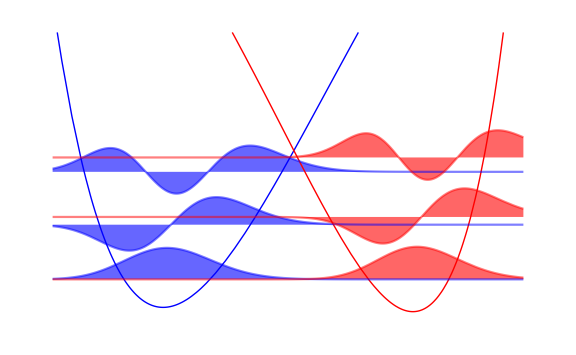

```mathematica
ROO=2.54;
Plot[
{
UR[x]-E1[0]au2kcal,
UP[x-R0[ROO]]-E2[0]au2kcal,
3ϕ1[x,0],3ϕ2[x-R0[ROO],0],
3ϕ1[x,1]+(E1[1]-E1[0])au2kcal,3ϕ2[x-R0[ROO],1]+(E2[1]-E2[0])au2kcal,
3ϕ1[x,2]+(E1[2]-E1[0])au2kcal,3ϕ2[x-R0[ROO],2]+(E2[2]-E2[0])au2kcal
},
{x,-0.5,R0[ROO]+0.5},
ImageSize->Large,
Axes->False,Frame->False,
PlotRange->{-7,40},
PlotStyle->{
{Blue,Thick},{Red,Thick},
{Blue,Opacity[0.5]},{Red,Opacity[0.5]},
{Blue,Opacity[0.5]},{Red,Opacity[0.5]},
{Blue,Opacity[0.5]},{Red,Opacity[0.5]}
},
Filling->{1->None,2->None,
3->0,4->0,
5->(E1[1]-E1[0])au2kcal,6->(E2[1]-E2[0])au2kcal,
7->(E1[2]-E1[0])au2kcal,8->(E2[2]-E2[0])au2kcal
},
FillingStyle->{
3->{Blue,Opacity[0.6]},4->{Red,Opacity[0.6]},
5->{Blue,Opacity[0.6]},6->{Red,Opacity[0.6]},
7->{Blue,Opacity[0.6]},8->{Red,Opacity[0.6]}
}
]
```

## Morse overlap integrals in terms of the Wigner function based on [J. C. Lopez, A. L. Rivera, Yu. F. Smirnov, A. Frank, arXiv:physics/0109017v]

General case:

```mathematica
FCH[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],
{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

```mathematica
FCD[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`50;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

Case β_1=β_2:

```mathematica
FC0H[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)
(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCH instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

```mathematica
FC0D[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCD instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

## Morse overlap integrals and their distance dependence

### Numerical overlap integrals

```mathematica
SH[R_,i_,j_]:=Module[{x,integrand},
integrand=SetAccuracy[ϕ1[x,i]ϕ2[-x+R,j],AccN];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->50,AccuracyGoal->30]];
```

```mathematica
SD[R_,i_,j_]:=Module[{x,integrand},
integrand=SetAccuracy[ϕ1D[x,i]ϕ2D[-x+R,j],AccN];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->50,AccuracyGoal->30]];
```

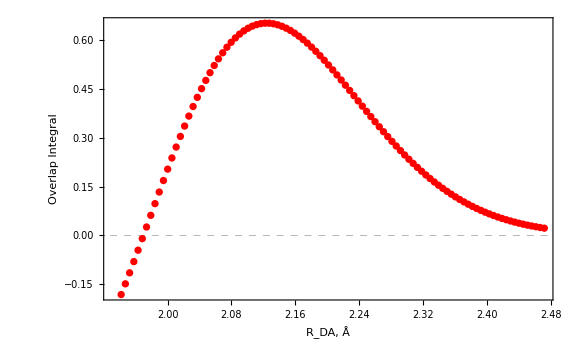

```mathematica
ListPlot[
Table[{RDA[x],SH[x,0,1]},{x,0,1,0.01}],
Axes->False,Frame->True,
FrameLabel->{"R_DA, Å","Overlap Integral"},
PlotStyle->{Black,Red},
PlotRange->All,ImageSize->Large,
GridLines->{None,{{0,Directive[Black,Dashed]}}}
]
```

### Spline all the distance dependencies

```mathematica
Clear[SHs,SHtable,SDs,SDtable];
Nbound=20;
Array[SHs,{Nbound+1,Nbound+1},{0,0}];
Array[SHtable,{Nbound+1,Nbound+1},{0,0}];
Array[SDs,{Nbound+1,Nbound+1},{0,0}];
Array[SDtable,{Nbound+1,Nbound+1},{0,0}];
```

### (! MUST BE REEVALUATED UPON CHANGING THE PROTON ACCEPTOR : CLICK ON THE RED BUTTON BELOW!)

```mathematica
Row[{
Button[Style["Spline overlap integrals and save to disk",Red],
progress="Calculating and splining proton overlaps: ";
Monitor[
Do[
SHtable[i,j]=ParallelTable[{Ri,SH[Ri,i,j]},{Ri,-2.0,4.0,0.005},ProgressReporting->False];
SHs[i,j]=Interpolation[SHtable[i,j],Method->"Spline",InterpolationOrder->3];
Put[SHs[i,j],"save/SHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,Nbound},{j,0,Nbound}
],
Row[{"Proton overlaps: ⟨",i,"|",j,"⟩"},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
Do[
SDtable[i,j]=ParallelTable[{Ri,SD[Ri,i,j]},{Ri,-2.0,4.0,0.005},ProgressReporting->False];
SDs[i,j]=Interpolation[SDtable[i,j],Method->"Spline",InterpolationOrder->3];
Put[SDs[i,j],"save/SDinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,Nbound},{j,0,Nbound}
],
Row[{"Deuteron overlaps: ⟨",i,"|",j,"⟩"},Frame->True,Background->Yellow,RoundingRadius->5]
],
Appearance->{"DialogBox"},Method->"Queued"
],
Button[Style["Read interpolation functions from disk",Blue],
Do[
SHs[i,j]=Get["save/SHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,Nbound},{j,0,Nbound}
];
Do[
SDs[i,j]=Get["save/SDinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,Nbound},{j,0,Nbound}
],
Appearance->{"DialogBox"},Method->"Queued"
]
}]
```

Spline overlap integrals and save to diskRead interpolation functions from disk

```mathematica
Manipulate[
ListPlot[
{Table[{RDA[x],SH[x,μ,ν]},{x,-2.,4.,0.1}],
Table[{RDA[x],SHs[μ,ν][x]},{x,-2.,4.,0.025}],
Table[{RDA[x],SD[x,μ,ν]},{x,-2.,4.,0.1}],
Table[{RDA[x],SDs[μ,ν][x]},{x,-2.,4.,0.025}]},
Axes->False,Frame->True,
FrameLabel->{"R_DA, Å","Overlap Integral"},
PlotStyle->{Red,Red,Blue,Blue},Joined->{False,True,False,True},
PlotRange->All,ImageSize->Large,
PlotLegends->Placed[LineLegend[{
"Numerical Overlap Integral (Hydrogen)",
"Splined Overlap Integral (Hydrogen)",
"Numerical Overlap Integral (Deuterium)",
"Splined Overlap Integral (Deuterium)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],Above]
],
{{μ,0,"Reactant quantum number"},Table[k,{k,0,Nbound}]},
{{ν,0,"Product quantum number"},Table[k,{k,0,Nbound}]},
ControlType->Setter
]
```

```mathematica
RDA[0]
```

1.942

## Overlap integrals for calculated proton potentials

### Proton potentials calculated at the reactant/product average geometries (from constrained optimizations)

```mathematica
RDAList=Range[2.14,3.14,0.1]
```

{2.14,2.24,2.34,2.44,2.54,2.64,2.74,2.84,2.94,3.04,3.14}

```mathematica
nRDA=Length[RDAList];
```

```mathematica
(*profileRctntFile=Table["data/profiles/RDA-"<>ToString[RDAList⟦i⟧]<>"00_averaged_Rctnt.dat",{i,1,nRDA}];*)
(*profilePrdctFile=Table["data/profiles/RDA-"<>ToString[RDAList⟦i⟧]<>"00_averaged_Prdct.dat",{i,1,nRDA}];*)
profileRctntFile=Table["data/profiles-adhoc/R"<>ToString[RDAList⟦i⟧]<>"00_aver-Hright_Rctnt.dat",{i,1,nRDA}];
profilePrdctFile=Table["data/profiles-adhoc/R"<>ToString[RDAList⟦i⟧]<>"00_aver-Hleft_Prdct.dat",{i,1,nRDA}];
```

```mathematica
profileRctntData=Table[MapAt[#*au2kcal&,ReadList[profileRctntFile⟦i⟧,{Real,Real}],{All,2}],{i,nRDA}];
profilePrdctData=Table[MapAt[#*au2kcal&,ReadList[profilePrdctFile⟦i⟧,{Real,Real}],{All,2}],{i,nRDA}];
```

```mathematica
plotOptions={Axes->False,Frame->True,InterpolationOrder->3,BaseStyle->{FontFamily->"Helvetica",FontSize->18},FrameStyle->Directive[Black,Thickness[Medium]],AspectRatio->0.75,PlotStyle->ReplacePart[Table[ColorData["Rainbow"][1-(RDAList⟦i⟧-RDAList⟦1⟧)/(RDAList⟦nRDA⟧-RDAList⟦1⟧)],{i,1,nRDA}],5->{Darker@ColorData["Rainbow"][1-(RDAList⟦5⟧-RDAList⟦1⟧)/(RDAList⟦nRDA⟧-RDAList⟦1⟧)],Thickness[0.01]}]};
```

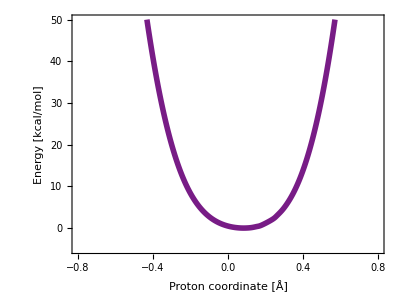

```mathematica
ListLinePlot[profileRctntData[[3]],
plotOptions,
PlotRange->{{-0.8,0.8},{-5,50}},
FrameLabel->{{"Energy [kcal/mol]",None},{"Proton coordinate [Å]","PT profiles in the Oxidized State\nRu(III)-OH...H-OH_2"}}
]
```

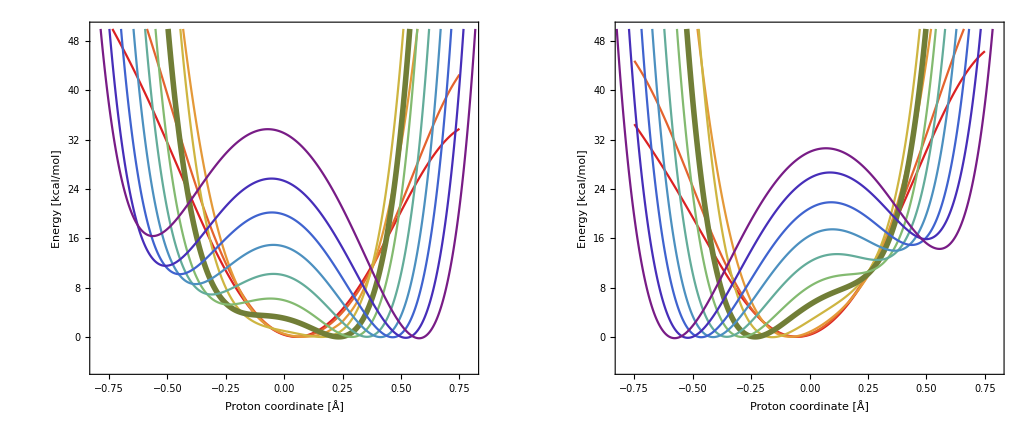

```mathematica
plotOptions={Axes->False,Frame->True,InterpolationOrder->3,BaseStyle->{FontFamily->"Helvetica",FontSize->18},FrameStyle->Directive[Black,Thickness[Medium]],AspectRatio->0.75,PlotStyle->ReplacePart[Table[ColorData["Rainbow"][1-(RDAList⟦i⟧-RDAList⟦1⟧)/(RDAList⟦nRDA⟧-RDAList⟦1⟧)],{i,1,nRDA}],5->{Darker@ColorData["Rainbow"][1-(RDAList⟦5⟧-RDAList⟦1⟧)/(RDAList⟦nRDA⟧-RDAList⟦1⟧)],Thickness[0.01]}]};
rctntPlots=ListLinePlot[profileRctntData,
plotOptions,
PlotRange->{{-0.8,0.8},{-5,50}},
FrameLabel->{{"Energy [kcal/mol]",None},{"Proton coordinate [Å]","PT profiles in the Oxidized State\nRu(III)-OH...H-OH_2"}}
];
prdctPlots=ListLinePlot[profilePrdctData,
plotOptions,
PlotRange->{{-0.8,0.8},{-5,50}},
FrameLabel->{{"Energy [kcal/mol]",None},{"Proton coordinate [Å]","PT profiles in the Reduced State\nRu(II)-OH-H...OH_2"}}
];
GraphicsRow[{
rctntPlots,prdctPlots,
LineLegend[Table[ColorData["Rainbow"][1-(RDAList⟦i⟧-RDAList⟦1⟧)/(RDAList⟦nRDA⟧-RDAList⟦1⟧)],{i,1,nRDA}],Table[ToString[RDAList⟦i⟧],{i,1,nRDA}],LegendLabel->Style["R_OO [Å]",18],LabelStyle->{Black,FontSize->16},LegendLayout->{"Column",1}]
},
ImageSize->1024]
```

Compose the files with both reactant and product potentials (in Hartrees) on the grid (for each DA distance)

```mathematica
profileData=Table[
MapThread[Append,{profileRctntData[[i]],profilePrdctData[[i,All,2]]}],
{i,1,nRDA}
];
profileDataHartrees=MapAt[#*kcal2au&,profileData,{All,All,{2,3}}];
```

```mathematica
filePotentialsau=Table["data/profiles-adhoc-colinear/RDA-"<>ToString[RDAList⟦i⟧]<>"00_averaged_au.dat",{i,1,nRDA}];
filePotentialskcal=Table["data/profiles-adhoc-colinear/RDA-"<>ToString[RDAList⟦i⟧]<>"00_averaged_kcal.dat",{i,1,nRDA}];
Do[
Export[filePotentialsau[[i]],profileDataHartrees[[i]],"Table"];
Export[filePotentialskcal[[i]],profileData[[i]],"Table"],
{i,1,nRDA}];
```

### Proton Vibrational Levels and Wavefunctions from 1D Schrödinger Equation

```mathematica
FGHWavefunctions::inputdata="The file `1` does not exist";
FGHWavefunctions::noexec="Executable not found";
FGHWavefunctions[file_,nGridPoints_,nStates_,OptionsPattern[{M->MassH}]]:=
Module[{BsplineCommand,mass,massString,filename,nG,nS,error,command,reactantEnergies,productEnergies,reactantPotential,productPotential,reactantWavefunctions,productWavefunctions,overlapMatrix,alphaMatrix},
BsplineCommand="/usr/local/bspline/bin/fgh_bspline.x";
filename=StringSplit[file,"."][[1]];
nG=nGridPoints;
(* Check if nStates < nGridPoints, otherwise set nStates to default value of 10 *)
If[nStates<nGridPoints,nS=nStates,nS=10];
mass=OptionValue[M]*Dalton;
massString=ToString[FortranForm[mass]];
(* run external executable to generate all the data *)
command=BsplineCommand<>" "<>file<>" "<>ToString[nG]<>" "<>massString<>" "<>ToString[nS]<>" > /dev/null";
error=Run[command];
If[error!=0,Message[FGHWavefunctions::noexec];Abort[]];
(* Read energies from disk *)
reactantEnergies=ReadList[filename<>"_reactant_en.dat",Real];
productEnergies=ReadList[filename<>"_product_en.dat",Real];
(* Read splined potentials from disk *)
reactantPotential=Part[ReadList[filename<>"_bspline.dat",{Number,Number,Number}],All,{1,2}];productPotential=Part[ReadList[filename<>"_bspline.dat",{Number,Number,Number}],All,{1,3}];
(* Read wavefunctions from disk *)
reactantWavefunctions={};
productWavefunctions={};
Do[reactantWavefunctions=Append[reactantWavefunctions,Part[ReadList[filename<>"_reactant_wf.dat",Table["Real",{k,1,1+nS}]],All,1+i]],{i,1,nS}];
Do[productWavefunctions=Append[productWavefunctions,Part[ReadList[filename<>"_product_wf.dat",Table["Real",{k,1,1+nS}]],All,1+i]],{i,1,nS}];(* Read overlap matrix from disk *)
overlapMatrix=ReadList[filename<>"_overlaps.dat",Table["Real",{k,1,nS}]];
(* Read alpha matrix from disk *)
alphaMatrix=ReadList[filename<>"_alphas.dat",Table["Real",{k,1,nS}]];
(* clean the data files in the current directory *)
DeleteFile[FileNames[filename<>"_*.dat"]];
(* Now gather all the results in one nested list *)
{{reactantEnergies,reactantPotential,reactantWavefunctions},{productEnergies,productPotential,productWavefunctions},overlapMatrix,alphaMatrix}
];
```

DVR direct, without Fourier Transform
(original code by Maxim Secor, 2019)

```mathematica
FGHMax[potx_,nGrid_,nRoots_,OptionsPattern[{M->MassH}]]:=Module[
{μ,potSpline,potxSplined,pot,xGrid,wavefunctions,k,xLeft,xRight,dx,KE,PE,Ham,energies,vectors},

μ=OptionValue[M]*Dalton;
potSpline=Interpolation[potx, Method->"Spline",InterpolationOrder->3];

(* calculate potential on the grid *)
xLeft=Min[potx[[All,1]]];
xRight=Max[potx[[All,1]]];
dx=(xRight-xLeft)/(nGrid-1);
xGrid=Table[x,{x,xLeft,xRight,dx}];
pot=Table[potSpline[x],{x,xLeft,xRight,dx}];
potxSplined=Table[{x,potSpline[x]au2kcal},{x,xLeft,xRight,dx}];

(*Construct kinetic and potential energy matrices*)
k=Pi/(dx a2bohr);
KE=Table[
1/(2μ) If[
i==j,k^2/3,
((2*k^2)/π^2)*(-1)^(i-j)/(i-j)^2
],
{i,0,nGrid-1},{j,0,nGrid-1}];
PE=DiagonalMatrix[pot];

(*Construct the Hamiltionian matrix and diagonalize*)
Ham=N[KE+PE];
energies = Reverse@Eigenvalues[Ham, -nRoots, Method -> {"Arnoldi", "Criteria" -> "RealPart"}];
vectors = Reverse@Eigenvectors[Ham, -nRoots, Method -> {"Arnoldi", "Criteria" -> "RealPart"}];
wavefunctions=Table[Table[{xGrid[[k]],vectors[[i,k]]},{k,1,nGrid}],{i,1,nRoots}];

(*Output*)
{energies*au2kcal,potxSplined,wavefunctions}
];
```

```mathematica
nRDA
```

11

```mathematica
RDAList
```

{2.14,2.24,2.34,2.44,2.54,2.64,2.74,2.84,2.94,3.04,3.14}

Calculate 10 quantum states in each potential:

```mathematica
FGHsolutionsH=Table[
FGHWavefunctions[filePotentialsau[[i]],512,10],
{i,1,nRDA}];
FGHsolutionsD=Table[
FGHWavefunctions[filePotentialsau[[i]],512,10,M->MassD],
{i,1,nRDA}];
```

### Spline DA distance dependence of the overlap integrals and energy levels

```mathematica
Clear[SHFGHs,SHFGHtable,SDFGHs,SDFGHtable];
Clear[E1HFGHs,E2HFGHs,E1HFGHtable,E2HFGHtable];
Clear[E1DFGHs,E2DFGHs,E1DFGHtable,E2DFGHtable];
NFGH=10;
Array[SHFGHs,{NFGH,NFGH},{0,0}];
Array[SHFGHtable,{NFGH,NFGH},{0,0}];
Array[SDFGHs,{NFGH,NFGH},{0,0}];
Array[SDFGHtable,{NFGH,NFGH},{0,0}];
Array[E1HFGHs,NFGH,0];
Array[E2HFGHs,NFGH,0];
Array[E1HFGHtable,NFGH,0];
Array[E2HFGHtable,NFGH,0];
Array[E1DFGHs,NFGH,0];
Array[E2DFGHs,NFGH,0];
Array[E1DFGHtable,NFGH,0];
Array[E2DFGHtable,NFGH,0];
```

```mathematica
FGHsolutionsH[[9,1,1,10]]
```

37.5077

```mathematica
Row[{
Button[Style["Spline FGH overlap integrals and Energy levels and save to disk",Red],
progress="Calculating and splining proton overlaps: ";
Monitor[
Do[
E1HFGHtable[j]=ParallelTable[{RDAList[[iR]],FGHsolutionsH[[iR,1,1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
E2HFGHtable[j]=ParallelTable[{RDAList[[iR]],FGHsolutionsH[[iR,2,1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
E1HFGHs[j]=Interpolation[E1HFGHtable[j],Method->"Spline",InterpolationOrder->2];
E2HFGHs[j]=Interpolation[E2HFGHtable[j],Method->"Spline",InterpolationOrder->2];
Put[E1HFGHs[j],"save/E1HFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Put[E2HFGHs[j],"save/E2HFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Do[
SHFGHtable[i,j]=ParallelTable[{RDAList[[iR]],FGHsolutionsH[[iR,3,i+1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
SHFGHs[i,j]=Interpolation[SHFGHtable[i,j],Method->"Spline",InterpolationOrder->2];
Put[SHFGHs[i,j],"save/SHFGHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,NFGH-1}],
{j,0,NFGH-1}
],
Row[{"Proton overlaps: ⟨",i,"|",j,"⟩"},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
Do[
E1DFGHtable[j]=ParallelTable[{RDAList[[iR]],FGHsolutionsD[[iR,1,1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
E2DFGHtable[j]=ParallelTable[{RDAList[[iR]],FGHsolutionsD[[iR,2,1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
E1DFGHs[j]=Interpolation[E1DFGHtable[j],Method->"Spline",InterpolationOrder->2];
E2DFGHs[j]=Interpolation[E2DFGHtable[j],Method->"Spline",InterpolationOrder->2];
Put[E1DFGHs[j],"save/E1DFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Put[E2DFGHs[j],"save/E2DFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Do[
SDFGHtable[i,j]=ParallelTable[{RDAList[[iR]],FGHsolutionsD[[iR,3,i+1,j+1]]},{iR,1,nRDA},ProgressReporting->False];
SDFGHs[i,j]=Interpolation[SDFGHtable[i,j],Method->"Spline",InterpolationOrder->2];
Put[SDFGHs[i,j],"save/SDFGHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,NFGH-1}],
{j,0,NFGH-1}
],
Row[{"Deuteron overlaps: ⟨",i,"|",j,"⟩"},Frame->True,Background->Yellow,RoundingRadius->5]
],
Appearance->{"DialogBox"},Method->"Queued"
],
Button[Style["Read interpolation functions from disk",Blue],
Do[
E1HFGHs[j]=Get["save/E1HFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
E2HFGHs[j]=Get["save/E2HFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Do[
SHFGHs[i,j]=Get["save/SHFGHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,NFGH-1}],
{j,0,NFGH-1}
];
Do[
E1DFGHs[j]=Get["save/E1DFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
E2DFGHs[j]=Get["save/E2DFGHinterpolated-"<>IntegerString[j,10,2]<>"-fun.dat"];
Do[
SDFGHs[i,j]=Get["save/SDFGHinterpolated-"<>IntegerString[i,10,2]<>"-"<>IntegerString[j,10,2]<>"-fun.dat"],
{i,0,NFGH-1}],
{j,0,NFGH-1}
],
Appearance->{"DialogBox"},Method->"Queued"
]
}]
```

Spline FGH overlap integrals and Energy levels and save to diskRead interpolation functions from disk

```mathematica
RDAList[[-1]]
```

3.14

```mathematica
FGHsolutionsH[[3,3,2,2]]
```

0.540605

```mathematica
Manipulate[
Row[{
ListPlot[
{Table[{RDAList[[iR]],FGHsolutionsH[[iR,3,μ+1,ν+1]]},{iR,1,nRDA}],
Table[{x,SHFGHs[μ,ν][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}],
Table[{RDAList[[iR]],FGHsolutionsD[[iR,3,μ+1,ν+1]]},{iR,1,nRDA}],
Table[{x,SDFGHs[μ,ν][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}]},
Axes->False,Frame->True,
BaseStyle->{14,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thickness[Medium]],
FrameLabel->{"R_DA, Å","Overlap Integral"},
PlotStyle->{Black,Black,{Black,Dashed},{Black,Dashed}},Joined->{False,True,False,True},
PlotRange->All,ImageSize->Large,
PlotLegends->Placed[LineLegend[{
"Numerical Overlap Integral (Hydrogen)",
"Splined Overlap Integral (Hydrogen)",
"Numerical Overlap Integral (Deuterium)",
"Splined Overlap Integral (Deuterium)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],Above]
],
ListPlot[
{Table[{RDAList[[iR]],FGHsolutionsH[[iR,1,1,μ+1]]},{iR,1,nRDA}],
Table[{RDAList[[iR]],FGHsolutionsH[[iR,2,1,ν+1]]},{iR,1,nRDA}],
Table[{x,E1HFGHs[μ][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}],
Table[{x,E2HFGHs[ν][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}],
Table[{RDAList[[iR]],FGHsolutionsD[[iR,1,1,μ+1]]},{iR,1,nRDA}],
Table[{RDAList[[iR]],FGHsolutionsD[[iR,2,1,ν+1]]},{iR,1,nRDA}],
Table[{x,E1DFGHs[μ][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}],
Table[{x,E2DFGHs[ν][x]},{x,RDAList[[1]],RDAList[[-1]],0.01}]},
Axes->False,Frame->True,
BaseStyle->{14,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thickness[Medium]],
FrameLabel->{"R_DA, Å","Energy Level, kcal/mol"},
PlotStyle->{Blue,Red,Blue,Red,{Blue,Dashed},{Red,Dashed},{Blue,Dashed},{Red,Dashed}},Joined->{False,False,True,True,False,False,True,True},
PlotRange->All,ImageSize->Large,
PlotLegends->Placed[LineLegend[{
"Numerical Reactant Energy Level (Hydrogen)",
"Numerical Product Energy Level (Hydrogen)",
"Splined Reactant Energy Level (Hydrogen)",
"Splined Product Energy Level (Hydrogen)",
"Numerical Reactant Energy Level (Deuteron)",
"Numerical Product Energy Level (Deuteron)",
"Splined Reactant Energy Level (Deuteron)",
"Splined Product Energy Level (Deuteron)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],Above]
]
},"      "],
{{μ,0,"Reactant quantum number"},Table[k,{k,0,NFGH-1}]},
{{ν,0,"Product quantum number"},Table[k,{k,0,NFGH-1}]},
ControlType->Setter
]
```

## Potential Dependent Rate Constants

```mathematica
(π V^2 Subscript[ρ, F] Subscript[P, μ] Subscript[S, μν]^2 erfc((Subscript[Δϵ, μν]+η+λ)/(2 √(λ kT))))/ℏ
```

## ET rate constants

```mathematica
kET[η_,λ_,T_,V_,ρF_]:=10^12 π/hbaraups V^2 ρF Erfc[(η ev2kcal+λ)/(2 √(kb T au2kcal λ))];
```

```mathematica
kETmax[V_,ρF_]:=10^12(2π)/hbaraups V^2 ρF;
```

```mathematica
knET[η_,λ_,T_]:=1/2 Erfc[(η ev2kcal+λ)/(2 √(kb T au2kcal λ))];
```

## PCET rate constants

```mathematica
kRPCET[η_,λ_,T_,V_,ρF_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,ϵμ,ϵν,Sμν,Erfcμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
sum=0;
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
ϵν=Which[
isotope=="H",( E2[ν]-E2[0])au2kcal,
isotope=="D",( E2D[ν]-E2D[0])au2kcal
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHs[μ,ν][R0[R]],
isotope=="D",SDs[μ,ν][R0[R]]
];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ (Sμν)^2 Erfcμν,
{ν,0,νmax},{μ,0,μmax}];
10^12 π/hbaraups V^2 ρF sum
];
```

```mathematica
kRFGHPCET[η_,λ_,T_,V_,ρF_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,ϵμ,ϵν,Sμν,Erfcμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1HFGHs[μ][R]-E1HFGHs[0][R])],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1DFGHs[μ][R]-E1DFGHs[0][R])],{μ,0,μmax}]
];
sum=0;
Do[
ϵμ=Which[
isotope=="H",E1HFGHs[μ][R]-E1HFGHs[0][R],
isotope=="D",E1DFGHs[μ][R]-E1DFGHs[0][R]
];
ϵν=Which[
isotope=="H",E2HFGHs[ν][R]-E2HFGHs[0][R],
isotope=="D",E2DFGHs[ν][R]-E2DFGHs[0][R]
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHFGHs[μ,ν][R],
isotope=="D",SDFGHs[μ,ν][R]
];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ (Sμν)^2 Erfcμν,
{ν,0,νmax},{μ,0,μmax}];
10^12 π/hbaraups V^2 ρF sum
];
```

```mathematica
kRPCETmax[T_,V_,ρF_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,ϵμ,Sμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
sum=0;
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHs[μ,ν][R0[R]],
isotope=="D",SDs[μ,ν][R0[R]]
];
sum+=Pμ (Sμν)^2,
{ν,0,νmax},{μ,0,μmax}];
10^12(2π)/hbaraups V^2 ρF sum
];
```

```mathematica
kRFGHPCETmax[T_,V_,ρF_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,ϵμ,Sμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1HFGHs[μ][R]-E1HFGHs[0][R])],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1DFGHs[μ][R]-E1DFGHs[0][R])],{μ,0,μmax}]
];
sum=0;
Do[
ϵμ=Which[
isotope=="H",E1HFGHs[μ][R]-E1HFGHs[0][R],
isotope=="D",E1DFGHs[μ][R]-E1DFGHs[0][R]
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHFGHs[μ,ν][R],
isotope=="D",SDFGHs[μ,ν][R]
];
sum+=Pμ (Sμν)^2,
{ν,0,νmax},{μ,0,μmax}];
10^12(2π)/hbaraups V^2 ρF sum
];
```

```mathematica
kRnPCET[η_,λ_,T_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,sumn,ϵμ,ϵν,Sμν,Erfcμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
sum=0;
sumn=0;
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
ϵν=Which[
isotope=="H",( E2[ν]-E2[0])au2kcal,
isotope=="D",( E2D[ν]-E2D[0])au2kcal
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHs[μ,ν][R0[R]],
isotope=="D",SDs[μ,ν][R0[R]]
];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ (Sμν)^2 Erfcμν;
sumn+=Pμ (Sμν)^2,
{ν,0,νmax},{μ,0,μmax}];
sum/(2sumn)
];
```

```mathematica
kRFGHnPCET[η_,λ_,T_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sum,sumn,ϵμ,ϵν,Sμν,Erfcμν},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1HFGHs[μ][R]-E1HFGHs[0][R])],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1DFGHs[μ][R]-E1DFGHs[0][R])],{μ,0,μmax}]
];
sum=0;
sumn=0;
Do[
ϵμ=Which[
isotope=="H",E1HFGHs[μ][R]-E1HFGHs[0][R],
isotope=="D",E1DFGHs[μ][R]-E1DFGHs[0][R]
];
ϵν=Which[
isotope=="H",E2HFGHs[ν][R]-E2HFGHs[0][R],
isotope=="D",E2DFGHs[ν][R]-E2DFGHs[0][R]
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHFGHs[μ,ν][R],
isotope=="D",SDFGHs[μ,ν][R]
];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ (Sμν)^2 Erfcμν;
sumn+=Pμ (Sμν)^2,
{ν,0,νmax},{μ,0,μmax}];
sum/(2sumn)
];
```

```mathematica
normR[T_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sumn,ϵμ,Sμν,cμνlist},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
sumn=0;
cμνlist={};
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHs[μ,ν][R0[R]],
isotope=="D",SDs[μ,ν][R0[R]]
];
AppendTo[cμνlist,Pμ Sμν^2];
sumn+=Pμ Sμν^2,
{ν,0,νmax},{μ,0,μmax}];
{cμνlist,sumn}
];
```

```mathematica
normRFGH[T_,R_,μmax_,νmax_,OptionsPattern[{Isotope->"H"}]]:=Module[
{isotope,β,Z,Pμ,sumn,ϵμ,Sμν,cμνlist},
isotope=OptionValue[Isotope];
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1HFGHs[μ][R]-E1HFGHs[0][R])],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1DFGHs[μ][R]-E1DFGHs[0][R])],{μ,0,μmax}]
];
sumn=0;
cμνlist={};
Do[
ϵμ=Which[
isotope=="H",E1HFGHs[μ][R]-E1HFGHs[0][R],
isotope=="D",E1DFGHs[μ][R]-E1DFGHs[0][R]
];
Pμ=Exp[-β ϵμ]/Z;
Sμν=Which[
isotope=="H",SHFGHs[μ,ν][R],
isotope=="D",SDFGHs[μ,ν][R]
];
AppendTo[cμνlist,Pμ Sμν^2];
sumn+=Pμ Sμν^2,
{ν,0,νmax},{μ,0,μmax}];
{cμνlist,sumn}
];
```

```mathematica
normRFGH[300,2.59,2,9]
```

{{0.0408832,0.00431721,1.32774×10^-7,0.4539,0.00062271,1.31879×10^-8,0.0000486026,0.000165766,2.39062×10^-6,0.258228,0.000646706,2.4593×10^-9,0.00926533,3.71403×10^-6,7.12218×10^-6,0.0000135764,8.85549×10^-6,2.37913×10^-6,7.33768×10^-6,4.00436×10^-7,2.77138×10^-7,1.05743×10^-7,1.5454×10^-7,7.96423×10^-10,2.72383×10^-6,1.94283×10^-9,6.25139×10^-10,2.18797×10^-7,5.29965×10^-10,4.0863×10^-11},0.768127}

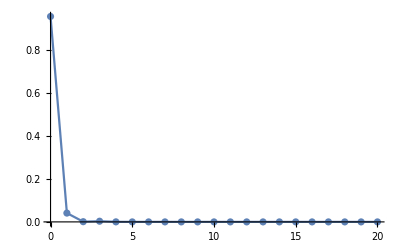

```mathematica
ListPlot[normR[300,2.0,0,20]⟦1⟧,DataRange->{0,20},PlotRange->All,Joined->True,Mesh->All]
```

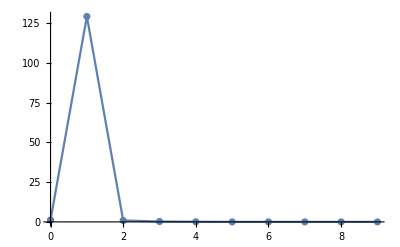

```mathematica
ListPlot[normRFGH[300,2.0,0,9]⟦1⟧,DataRange->{0,9},PlotRange->All,Joined->True,Mesh->All]
```

```mathematica
normR[300,2.54,0,20]
```

{{1.37297×10^-6,0.0000404747,0.000565745,0.00480919,0.0267905,0.0989992,0.235712,0.334778,0.239199,0.0526092,0.000307983,0.00533184,0.0000136021,0.000605511,0.000131428,7.43314×10^-6,0.0000477515,0.0000288869,7.57625×10^-6,7.73377×10^-7,2.55487×10^-9},0.999987}

```mathematica
normRFGH[300,2.94,0,9]
```

{{3.60258×10^-9,9.88312×10^-7,0.200143,0.722729,0.0396068,0.0317122,0.00520454,0.000574216,9.15586×10^-6,7.42923×10^-6},0.999988}

```mathematica
ListPlot[Table[{νmax,kRFGHPCET[-10,λETcalc,300,1,1,2.54,1,νmax]},{νmax,0,9}]]
```

-Graphics-

```mathematica
kRnPCET[-5,λETcalc,300,2.54,1,11]
```

1.

```mathematica
kRFGHnPCET[-5,λETcalc,300,2.54,1,9]
```

1.

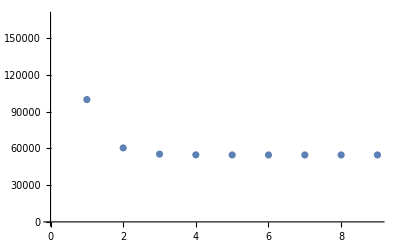

```mathematica
ListPlot[Table[{νmax,10^8 kRFGHnPCET[0,λETcalc,300,2.54,1,νmax]},{νmax,0,9,1}]]
```

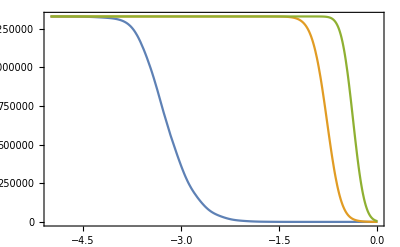

```mathematica
Plot[
{kRPCET[η,λETcalc,300,VET,ρF,2.6,9,20],
kRFGHPCET[η,λETcalc,300,VET,ρF,2.64,9,9],
kET[η,λETcalc,300,VET,ρF]},
{η,-5,0},
Axes->False,Frame->True,
PlotRange->All
]
```

```mathematica
gbvf
```

## k-η Plots at a fixed DA distance

```mathematica
T=300;
Manipulate[
Plot[{
10^-6 kET[-η,λETcalc,T,VET,ρF],
10^-6 kRPCET[-η,λETcalc,T,VET,ρF,ROO,μmax,νmax],
10^-6 kRFGHPCET[-η,λETcalc,T,VET,ρF,ROO,μmax,νmax]
},{η,-0.5,5},
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,Red,{Red,Dashed}},
BaseStyle->{FontSize->18},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k×10^-6 [s^-1]"},
GridLines->{{{λETcalc,Black}},None},
GridLinesStyle->Directive[Thick,Dashed],
Epilog->{Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λETcalc-0.12,0.2}]}
],
{{ROO,2.54,"Proton donor-acceptor distance (Å)"},2,3.5,0.1,Appearance->"Open"},
{{μmax,0,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,0,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Red,FontSize->14}
]
```

```mathematica
λPCETcalc kcal2ev
```

0.748464

```mathematica
T=300;
Manipulate[
Plot[{
knET[-η,λET ev2kcal,T],
kRnPCET[-η,λPCET ev2kcal,T,ROO,μmax,νmax],
kRFGHnPCET[-η,λPCET ev2kcal,T,ROO,μmax,νmax],
knET[-η,λapp ev2kcal,T]},
{η,-0.2,3.0},
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,Red,{Red,Dashed},{Black,Dashed}},
LabelStyle->{Black,FontSize->16},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k/k_max"},
FrameStyle->Directive[Black,Thickness[Medium]],
GridLines->{{{λET,Black},{λapp,Red}},{{0.5,Thin}}},
GridLinesStyle->Directive[Thick,Dashed],
PlotLegends->Placed[{"ET","PCET(Morse)","PCET(FGH)","Single term (ET) fit"},{0.7,0.25}],
Epilog->{
{PointSize->Large,Point[knETdata]},{PointSize->Large,Red,Point[knPCETdata]},
Text[Style["● ET (experiment)",16,Black,FontFamily->"Helvetica",Background->White],{1.75,0.8},{-1,0}],
Text[Style["● PCET (experiment)",16,Red,FontFamily->"Helvetica",Background->White],{1.75,0.7},{-1,0}],
Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λET-0.2,0.5}],
Text[Style["λ_app = "<>ToString[NumberForm[λapp,3]]<>" eV",24,Red,FontFamily->"Times",Background->White],{λapp+0.5,0.5}],
{Arrowheads[Medium],Background->Transparent,Arrow[{{λET,0.5},{λapp,0.5}}]}
}
],
{{ROO,2.54,"Proton donor-acceptor distance (Å)"},2.14,3.14,0.05,Appearance->"Open"},
{{λET,λETcalc kcal2ev,"ET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λPCET,λPCETcalc kcal2ev,"PCET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λapp,λPCETobs kcal2ev,"Apparent reorganization energy (eV)"},λET,2.5,0.01,Appearance->"Open"},
{{μmax,0,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,0,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Black,FontSize->14}
]
```

## Potential along the DA distance

Q-Chem constrained optimization results (Å, Hartrees):

```mathematica
qchemROOrawdata={
{2.1400,-2772.5126960958},
{2.2400,-2772.5250568553},
{2.3400,-2772.5315358503},
{2.4400,-2772.5340540525},
{2.5400,-2772.5347405595},
{2.6400,-2772.5342755661},
{2.7400,-2772.5331012925},
{2.8400,-2772.5315056016},
{2.9400,-2772.5297511109},
{3.0400,-2772.5279938980},
{3.1400,-2772.5267975765}
};
```

```mathematica
energyMin=Min[qchemROOrawdata⟦All,2⟧]
ROOmin=qchemROOrawdata⟦Position[qchemROOrawdata,energyMin]⟦1,1⟧,1⟧
```

-2772.53

2.54

```mathematica
qchemROOdata=MapAt[(#-energyMin)au2kcal&,qchemROOrawdata,{All,2}];
```

### Quadratic fit with a fixed minimum:

```mathematica
Clear[UROOharm,fOO]
```

```mathematica
UROOharm=NonlinearModelFit[qchemROOdata,1/2 fR(x-ROOmin)^2,{{fR,1}},x]
```

FittedModel[24.4405 (-2.54+x)^2]

```mathematica
fOO=UROOharm["BestFitParameters"]⟦1,2⟧
```

48.8809

```mathematica
Integrate[Exp[-β/2 f(x-x0)^2],{x,-∞,∞},Assumptions->{β>0,f>0,x0∈Reals}]
```

(√(2 π))/(√(f β))

```mathematica
Nharm[T_]:=√((2 π kb T au2kcal)/fOO);
```

```mathematica
Pharm[T_,R_]:=1/Nharm[T] Exp[-UROOharm[R]/(kb T au2kcal)];
```

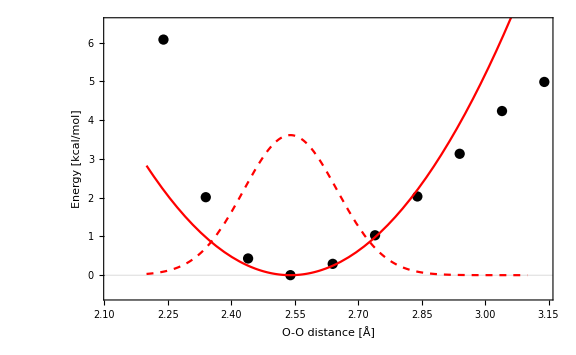

```mathematica
Show[
ListPlot[qchemROOdata,
PlotRange->{-0.5,6.5},
Axes->False,Frame->True,
ImageSize->Large,
FrameStyle->{Black,Thickness[0.0025]},
LabelStyle->{Black,FontSize->18},
FrameLabel->{{"Energy [kcal/mol]","P(R_OO) [Å^-1]"},{"O-O distance [Å]",None}},
GridLines->{None,{0}},
PlotStyle->Black
],
Plot[{Pharm[300,R],UROOharm[R]},{R,2.2,3.1},PlotStyle->{{Red,Dashed},Red}]
]
```

### Spline interpolation:

```mathematica
UROOspline=Interpolation[qchemROOdata,Method->"Spline",InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
Nspline[T_,Rleft_,Rright_]:=Nspline[T,Rleft,Rright]=NIntegrate[Exp[-UROOspline[R]/(kb T au2kcal)],{R,Rleft,Rright}];
```

```mathematica
Pspline[T_,Rleft_,Rright_,R_]:=Pspline[T,Rleft,Rright,R]=1/Nspline[T,Rleft,Rright] Exp[-UROOspline[R]/(kb T au2kcal)];
```

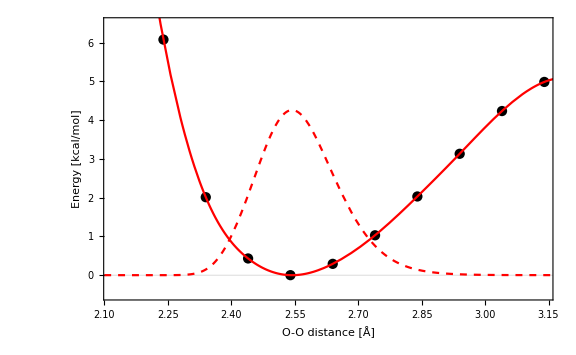

```mathematica
Show[
ListPlot[qchemROOdata,
PlotRange->{-0.5,6.5},
Axes->False,Frame->True,
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[Medium]],
LabelStyle->{Black,FontSize->18},
FrameLabel->{{"Energy [kcal/mol]","P(R_OO) [Å^-1]"},{"O-O distance [Å]",None}},
GridLines->{None,{0}},
PlotStyle->Black
],
Plot[{Pspline[300,2.2,3.2,R],UROOspline[R]},{R,2.1,3.2},PlotStyle->{{Red,Dashed},Red}]
]
```

### Fit to Morse potential

```mathematica
UROOmorse=NonlinearModelFit[qchemROOdata,DOO(1-Exp[-βOO(x-ROOmin)])^2,{{DOO,100},{βOO,2}},x]
```

FittedModel[11.0941 (1-ⅇ^(-1.8693 (-2.54+x)))^2]

```mathematica
Normal[UROOmorse]/.{x->R}
```

11.0941 (1-ⅇ^(-1.8693 (-2.54+R)))^2

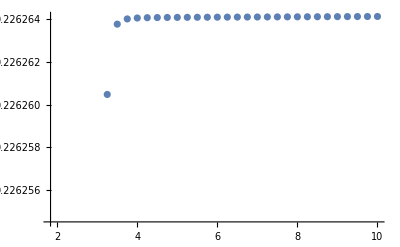

```mathematica
ListPlot[Table[{R2,NIntegrate[Exp[-UROOmorse[R]/(kb T au2kcal)],{R,0,R2}]},{R2,2,10,0.25}]]
```

```mathematica
Nmorse[T_,Rleft_,Rright_]:=Nmorse[T,Rleft,Rright]=NIntegrate[Exp[-UROOmorse[R]/(kb T au2kcal)],{R,Rleft,Rright}];
```

```mathematica
Pmorse[T_,Rleft_,Rright_,R_]:=1/Nmorse[T,Rleft,Rright] Exp[-UROOmorse[R]/(kb T au2kcal)];
```

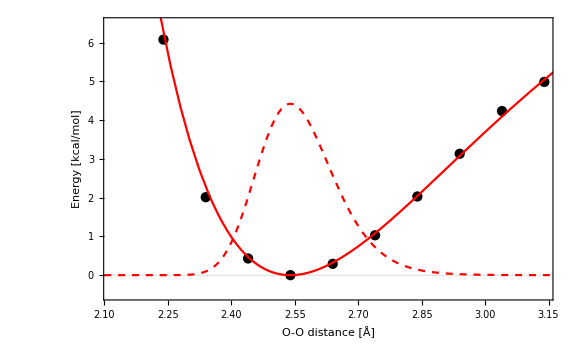

```mathematica
Show[
ListPlot[qchemROOdata,
PlotRange->{-0.5,6.5},
Axes->False,Frame->True,
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[Medium]],
LabelStyle->{Black,FontSize->18},
FrameLabel->{{"Energy [kcal/mol]","P(R_OO) [Å^-1]"},{"O-O distance [Å]",None}},
GridLines->{None,{0}},
PlotStyle->Black
],
Plot[{Pmorse[300,0,5,R],UROOmorse[R]},{R,2.1,3.2},PlotStyle->{{Red,Dashed},Red}]
]
```

## PCET rate constants with averaging over DA distance (Hydrogen only at this point)

### With Morse Proton Potentials

```mathematica
kPCETharmR[η_,λ_,T_,V_,ρF_,μmax_,νmax_]:=kPCETharmR[η,λ,T,V,ρF,μmax,νmax]=Module[
{isotope,β,Z,Pμ,sum,ϵμ,ϵν,PSμν2,Sμν2av,Erfcμν},
β=1/(kb T au2kcal);
Z=Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}];
sum=0;
Do[
ϵμ=( E1[μ]-E1[0])au2kcal;
ϵν=( E2[ν]-E2[0])au2kcal;
Pμ=Exp[-β ϵμ]/Z;
PSμν2[R_?NumericQ]:=Pharm[T,R]×(SHs[μ,ν][R0[R]])^2;
Sμν2av=NIntegrate[PSμν2[x],{x,0,10},Method->{Automatic,"SymbolicProcessing"->0}];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ Sμν2av Erfcμν,
{ν,0,νmax},{μ,0,μmax}];
10^12 π/hbaraups V^2 ρF sum
];
```

```mathematica
kPCETharmRmax[T_,V_,ρF_,μmax_,νmax_]:=kPCETharmRmax[T,V,ρF,μmax,νmax]=Module[
{isotope,β,Z,Pμ,sumn,ϵμ,Sμν2av,PSμν2},
β=1/(kb T au2kcal);
Z=Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}];
sumn=0;
Do[
ϵμ=( E1[μ]-E1[0])au2kcal;
Pμ=Exp[-β ϵμ]/Z;
PSμν2[R_?NumericQ]:=Pharm[T,R]×(SHs[μ,ν][R0[R]])^2;
Sμν2av=NIntegrate[PSμν2[x],{x,0,10},Method->{Automatic,"SymbolicProcessing"->0}];
sumn+=Pμ Sμν2av,
{ν,0,νmax},{μ,0,μmax}];
10^12(2π)/hbaraups V^2 ρF sumn
];
```

```mathematica
knPCETharmR[η_,λ_,T_,μmax_,νmax_]:=knPCETharmR[η,λ,T,μmax,νmax]=Module[
{isotope,β,Z,Pμ,sum,sumn,ϵμ,ϵν,Sμν2av,PSμν2,Erfcμν},
β=1/(kb T au2kcal);
Z=Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}];
sum=0;
sumn=0;
Do[
ϵμ=( E1[μ]-E1[0])au2kcal;
ϵν=( E2[ν]-E2[0])au2kcal;
Pμ=Exp[-β ϵμ]/Z;
PSμν2[R_?NumericQ]:=Pharm[T,R]×(SHs[μ,ν][R0[R]])^2;
Sμν2av=NIntegrate[PSμν2[x],{x,0,10},Method->{Automatic,"SymbolicProcessing"->0}];
Erfcμν=Erfc[(η ev2kcal+ϵν-ϵμ+λ)/(2 √(kb T au2kcal λ))];
sum+=Pμ Sμν2av Erfcμν;
sumn+=Pμ Sμν2av,
{ν,0,νmax},{μ,0,μmax}];
sum/(2sumn)
];
```

```mathematica
kPCETharmR[-5,λPCETcalc,300,VET,ρF,20,20]
```

1.3269×10^6

```mathematica
kET[-5,λETcalc,300,VET,ρF]
```

1.32884×10^6

```mathematica
Table[{νmax,kPCETharmR[-0.5,λETcalc,300,VET,ρF,0,νmax]},{νmax,0,10}]//TableForm
```

0 | 717.141
1 | 777.596
2 | 777.597
3 | 777.597
4 | 777.597
5 | 777.597
6 | 777.597
7 | 777.597
8 | 777.597
9 | 777.597
10 | 777.597

```mathematica
knPCETharmR[0,λETcalc,300,1,9]
```

2.56873×10^-6

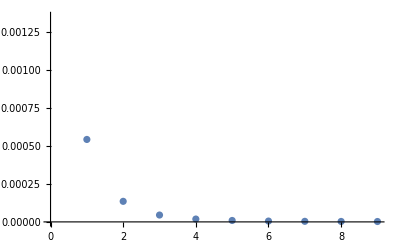

```mathematica
ListPlot[Table[{νmax,knPCETharmR[0,λETcalc,300,1,νmax]},{νmax,0,9,1}]]
```

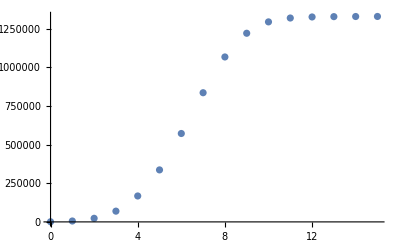

```mathematica
ListPlot[Table[{νmax,kPCETharmRmax[300,VET,ρF,1,νmax]},{νmax,0,15,1}]]
```

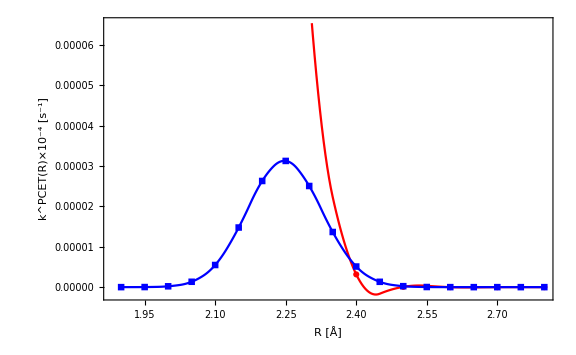

```mathematica
ListLinePlot[{
Table[{R,10^-4 kRPCET[0,λPCETcalc,300,VET,ρF,R,1,10]},{R,2.1,2.8,0.1}],
Table[{R,Pharm[300,R]×10^-4×kRPCET[0,λPCETcalc,300,VET,ρF,R,1,10]},{R,1.9,2.8,0.05}]
},
ImageSize->Large,
PlotStyle->{Red,Blue},
Frame->True,Axes->False,
FrameStyle->{Black,Thickness->0.0025},
FrameLabel->{{Style["k^PCET(R)×10^-4 [s^-1]",Red],Style["k^PCET(R)P(R)×10^-4 [s^-1Å^-1]",Blue]},{"R [Å]",None}},
LabelStyle->{16,Black},
PlotMarkers->Automatic,
InterpolationOrder->2
]
```

```mathematica
T=300;
Manipulate[
Plot[
{kET[-η,λETcalc,T,VET,ρF],kPCETharmR[-η,λPCETcalc,T,VET,ρF,μmax,νmax]},{η,-0.5,5},
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,{Red,Dashed},Red},
BaseStyle->{FontSize->18},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k [s^-1]"},
GridLines->{{{λETcalc kcal2ev,Black}},None},
GridLinesStyle->Directive[Thick,Dashed],
Epilog->{Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λETcalc kcal2ev-0.12,0.2}]}
],
{{μmax,0,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,0,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Red,FontSize->16}
]
```

```mathematica
λETcalc kcal2ev
```

0.374232

```mathematica
T=300;
Manipulate[
Plot[{knET[-η,λET ev2kcal,T],knPCETharmR[-η,λPCET ev2kcal,T,μmax,νmax],knET[-η,λapp ev2kcal,T]},{η,-0.2,3.0},
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,Red,{Red,Dashed}},
LabelStyle->{Black,FontSize->16},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k/k_max"},
FrameStyle->{Black},
GridLines->{{{λET,Black},{λapp,Red}},{{0.5,Thin}}},
GridLinesStyle->Directive[Thick,Dashed],
PlotLegends->Placed[{"ET","PCET (Morse)","Single term (ET) fit"},{0.6,0.25}],
Epilog->{
{PointSize->Large,Point[knETdata]},{PointSize->Large,Red,Point[knPCETdata]},
Text[Style["● ET (experiment)",16,Black,FontFamily->"Helvetica",Background->White],{1.75,0.8},{-1,0}],
Text[Style["● PCET (experiment)",16,Red,FontFamily->"Helvetica",Background->White],{1.75,0.7},{-1,0}],
Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λET-0.2,0.5}],
Text[Style["λ_app = "<>ToString[NumberForm[λapp,2]]<>" eV",24,Red,FontFamily->"Times",Background->White],{λapp+0.5,0.5}],
{Arrowheads[Medium],Background->Transparent,Arrow[{{λET,0.5},{λapp,0.5}}]}
}
],
{{λET,λETcalc×kcal2ev,"ET reorganization energy (eV)"},5kcal2ev,2,0.01,Appearance->"Open"},
{{λPCET,λPCETcalc×kcal2ev,"PCET reorganization energy (eV)"},15kcal2ev,2,0.01,Appearance->"Open"},
{{λapp,λPCETobs kcal2ev,"Apparent reorganization energy (eV)"},λET,2.5,0.01,Appearance->"Open"},
{{μmax,0,"Highest reactant proton vibrational state"},Table[k,{k,0,10}],ControlType->Setter},
{{νmax,0,"Highest product proton vibrational state"},Table[k,{k,0,10}],ControlType->Setter},
LabelStyle->{Black,FontSize->14}
]
```

### With Calculated Proton Potentials and FGH wavefunctions

```mathematica
kFGHPCETharmR[η_,λ_,T_,V_,ρF_,μmax_,νmax_]:=kFGHPCETharmR[η,λ,T,V,ρF,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pharm[T,R]×kRFGHPCET[η,λ,T,V,ρF,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
kFGHPCETharmRmax[T_,V_,ρF_,μmax_,νmax_]:=kFGHPCETharmRmax[T,V,ρF,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pharm[T,R]×kRFGHPCETmax[T,V,ρF,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
knFGHPCETharmR[η_,λ_,T_,μmax_,νmax_]:=knFGHPCETharmR[η,λ,T,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pharm[T,R]×kRFGHnPCET[η,λ,T,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
kFGHPCETsplineR[η_,λ_,T_,V_,ρF_,μmax_,νmax_]:=kFGHPCETsplineR[η,λ,T,V,ρF,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pspline[T,Rmin,Rmax,R]×kRFGHPCET[η,λ,T,V,ρF,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
kFGHPCETsplineRmax[T_,V_,ρF_,μmax_,νmax_]:=kFGHPCETsplineRmax[T,V,ρF,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pspline[T,Rmin,Rmax,R]×kRFGHPCETmax[T,V,ρF,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
knFGHPCETsplineR[η_,λ_,T_,μmax_,νmax_]:=knFGHPCETsplineR[η,λ,T,μmax,νmax]=Module[
{Pk,Rmin,Rmax},
Rmin=RDAList[[1]];
Rmax=RDAList[[-1]];
Pk[R_?NumericQ]:=Pspline[T,Rmin,Rmax,R]×kRFGHnPCET[η,λ,T,R,μmax,νmax];
NIntegrate[Pk[x],{x,Rmin,Rmax},Method->{Automatic,"SymbolicProcessing"->0}]
];
```

```mathematica
kFGHPCETharmR[-2,λETcalc,300,VET,ρF,2,9]
```

1.15536×10^6

```mathematica
kET[-2,λETcalc,300,VET,ρF]
```

1.32884×10^6

```mathematica
kFGHPCETsplineR[-2,λETcalc,300,VET,ρF,1,9]
```

1.12329×10^6

```mathematica
Table[{νmax,kFGHPCETharmR[-0.5,λETcalc,300,VET,ρF,0,νmax]},{νmax,0,9}]//TableForm
```

0 | 216183.
1 | 313344.
2 | 322112.
3 | 322302.
4 | 322303.
5 | 322303.
6 | 322303.
7 | 322303.
8 | 322303.
9 | 322303.

```mathematica
knFGHPCETharmR[0,λETcalc,300,1,9]
```

0.00102391

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.94663}. NIntegrate obtained 0.00159379 and 4.71279×10^-9 for the integral and error estimates.

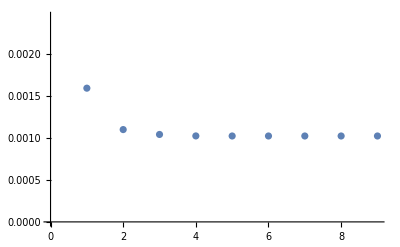

```mathematica
ListPlot[Table[{νmax,knFGHPCETharmR[0,λETcalc,300,1,νmax]},{νmax,0,9,1}]]
```

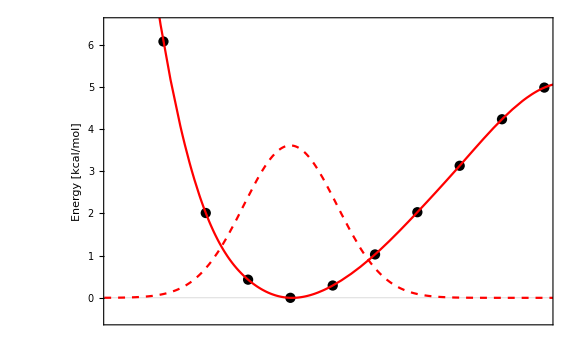

```mathematica
figS6up=Show[
ListPlot[qchemROOdata,
PlotRange->{-0.5,6.5},
Axes->False,Frame->True,
ImageSize->Large,
FrameStyle->Directive[Black,Thickness[Medium]],
LabelStyle->{Black,FontSize->24},
FrameLabel->{{"Energy [kcal/mol]","P(R_OO) [Å^-1]"},{None,None}},
FrameTicks->{
{
{2.2,Spacer[0]},
{2.3,Spacer[0]},
{2.4,Spacer[0]},
{2.5,Spacer[0]},
{2.6,Spacer[0]},
{2.7,Spacer[0]},
{2.8,Spacer[0]},
{2.9,Spacer[0]},
{3.0,Spacer[0]},
{3.1,Spacer[0]}
},
Automatic},
GridLines->{None,{0}},
PlotStyle->Black
],
Plot[{Pharm[300,R],UROOspline[R]},{R,2.1,3.2},PlotStyle->{{Red,Dashed},Red}]
]
```

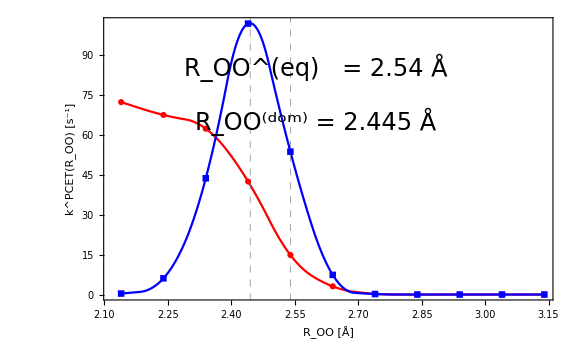

```mathematica
figS6down=ListLinePlot[{
Table[{R,kRFGHPCET[0,λPCETcalc,300,VET,ρF,R,1,9]},{R,2.14,3.14,0.1}],
Table[{R,Pharm[300,R]×kRFGHPCET[0,λPCETcalc,300,VET,ρF,R,1,9]},{R,2.14,3.14,0.1}]
},
ImageSize->Large,
PlotStyle->{Red,Blue},
Frame->True,Axes->False,
FrameStyle->Directive[Black,Thickness[Medium]],
FrameLabel->{{Style["k^PCET(R_OO) [s^-1]",Red],Style["k^PCET(R_OO) P(R_OO) [s^-1Å^-1]",Blue]},{"R_OO [Å]",None}},
LabelStyle->{24,Black},
PlotMarkers->Automatic,
InterpolationOrder->2,
GridLines->{{2.445,RDAList[[5]]},None},
GridLinesStyle->Directive[Gray, Dashed,Thickness[Medium]],
Epilog->{
Text[Style["R_OO^(eq)   = "<>ToString[RDAList[[5]]]<>" Å ",24,Black,FontFamily->"Helvetica",Background->White],{2.6,85},{-1,0}],
Text[Style["R_OO^(dom) = "<>ToString[2.445]<>" Å ",24,Black,FontFamily->"Helvetica",Background->White],{2.6,65},{-1,0}]
}
]
```

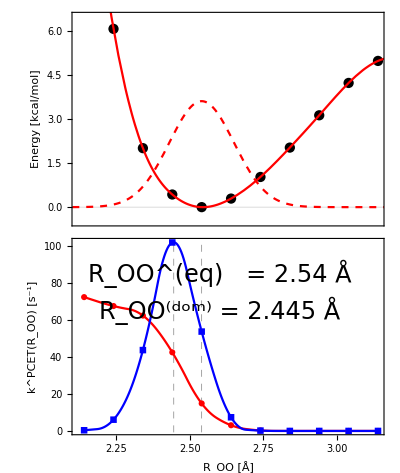

```mathematica
GraphicsGrid[{{figS6up},{figS6down}},Spacings->-30]
```

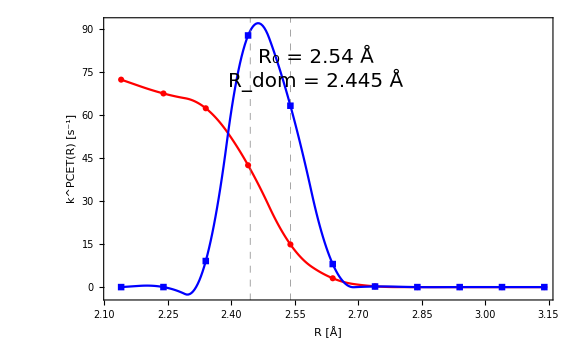

```mathematica
ListLinePlot[{
Table[{R,kRFGHPCET[0,λPCETcalc,300,VET,ρF,R,1,9]},{R,2.14,3.14,0.1}],
Table[{R,Pspline[300,RDAList[[1]],RDAList[[-1]],R]×kRFGHPCET[0,λPCETcalc,300,VET,ρF,R,1,9]},{R,2.14,3.14,0.1}]
},
ImageSize->Large,
PlotStyle->{Red,Blue},
Frame->True,Axes->False,
FrameStyle->Directive[Black,Thickness[Medium]],
FrameLabel->{{Style["k^PCET(R) [s^-1]",Red],Style["k^PCET(R) P(R) [s^-1Å^-1]",Blue]},{"R [Å]",None}},
LabelStyle->{20,Black},
PlotMarkers->Automatic,
InterpolationOrder->2,
GridLines->{{2.445,RDAList[[5]]},None},
GridLinesStyle->Directive[Gray, Dashed,Thickness[Medium]],
Epilog->{
Text[Style["R_0 = "<>ToString[RDAList[[5]]]<>" Å ",20,Black,FontFamily->"Helvetica",Background->White],{2.6,80},{-1,0}],
Text[Style["R_dom = "<>ToString[2.445]<>" Å ",20,Black,FontFamily->"Helvetica",Background->White],{2.6,72},{-1,0}]
}
]
```

```mathematica
{λETcalc,λPCETcalc}
```

{8.63,17.26}

```mathematica
T=300;
Manipulate[
Plot[
{
10^-6 kET[-η,λETcalc,T,VET,ρF],
10^-6 kFGHPCETharmR[-η,λETcalc,T,VET,ρF,μmax,νmax]
},
{η,-0.5,5},
PlotPoints->10,MaxRecursion->3,
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,{Red,Dashed},Red},
BaseStyle->{FontSize->18},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k×10^-6 [s^-1]"},
GridLines->{{{λETcalc kcal2ev,Black}},None},
GridLinesStyle->Directive[Thick,Dashed],
Epilog->{Text[Style["λ_ET",24,Black,FontFamily->"Times",Background->White],{λETcalc kcal2ev-0.12,0.2}]}
],
{{μmax,0,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,0,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Red,FontSize->14}
]
```

```mathematica
T=300;
Manipulate[
Plot[{knET[-η,λET ev2kcal,T],knFGHPCETharmR[-η,λPCET ev2kcal,T,μmax,νmax],knET[-η,λapp ev2kcal,T]},{η,-0.2,3.0},
PlotPoints->10,MaxRecursion->3,
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,Red,{White,Transparent,Dashed}},
LabelStyle->{Black,FontSize->20},
Axes->False,Frame->True,
FrameLabel->{"-ΔG^o [eV]","k/k_max"},
FrameStyle->Directive[Black,Thickness[Medium]],
GridLines->{{{λET,Black},{λapp,Red}},{{0.5,Thin}}},
GridLinesStyle->Directive[Thick,Dashed],
PlotLegends->Placed[{"ET (theory)","PCET (theory)"},{0.75,0.2}],
Epilog->{
{PointSize->Large,Point[knETdata]},{PointSize->Large,Red,Point[knPCETdata]},
Text[Style["● ET (experiment)",20,Black,FontFamily->"Helvetica",Background->White],{1.7,0.85},{-1,0}],
Text[Style["● PCET (experiment)",20,Red,FontFamily->"Helvetica",Background->White],{1.7,0.72},{-1,0}],
Text[Style["λ_ET",24,Black,FontFamily->"Helvetica",Background->White],{λET-0.2,0.5}],
Text[Style["λ_PCET^app = "<>ToString[NumberForm[λapp,3]]<>" eV",24,Red,FontFamily->"Helvetica",Background->White],{λapp+0.6,0.5}],
{Arrowheads[Medium],Red,Background->Transparent,Thick,Arrow@Line[{{λET,0.5},{λapp,0.5}},VertexColors->{Black,Red}]}
}
],
{{λET,λETcalc kcal2ev,"ET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λPCET,λPCETcalc kcal2ev,"PCET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λapp,1.01,"Apparent reorganization energy (eV)"},λET,2.5,0.01,Appearance->"Open"},
{{μmax,1,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,7,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Black,FontSize->14}
]
```

```mathematica
λPCETinner kcal2ev
```

0.537281

With splined P(R):

```mathematica
T=300;
Manipulate[
Plot[{knET[-η,λET ev2kcal,T],knFGHPCETsplineR[-η,λPCET ev2kcal,T,μmax,νmax],knET[-η,λapp ev2kcal,T]},{η,-0.2,3.0},
PlotPoints->10,MaxRecursion->3,
PlotRange->All,ImageSize->Large,
PlotStyle->{Black,Red,{Red,Transparent,Dashed}},
LabelStyle->{Black,FontSize->20},
Axes->False,Frame->True,
FrameLabel->{"-G [eV]","k/k_max"},
FrameStyle->Directive[Black,Thickness[Medium]],
GridLines->{{{λET,Black},{λapp,Red}},{{0.5,Thin}}},
GridLinesStyle->Directive[Thick,Dashed],
PlotLegends->Placed[{"ET (theory)","PCET (theory)"},{0.75,0.2}],
Epilog->{
{PointSize->Large,Point[knETdata]},{PointSize->Large,Red,Point[knPCETdata]},
Text[Style["● ET (experiment)",20,Black,FontFamily->"Helvetica",Background->White],{1.75,0.82},{-1,0}],
Text[Style["● PCET (experiment)",20,Red,FontFamily->"Helvetica",Background->White],{1.75,0.7},{-1,0}],
Text[Style["λ_ET",24,Black,FontFamily->"Helvetica",Background->White],{λET-0.2,0.5}],
Text[Style["λ_PCET^app = "<>ToString[NumberForm[λapp,3]]<>" eV",24,Red,FontFamily->"Helvetica",Background->White],{λapp+0.6,0.5}],
{Arrowheads[Medium],Red,Background->Transparent,Thick,Arrow@Line[{{λET,0.5},{λapp,0.5}},VertexColors->{Black,Red}]}
}
],
{{λET,λETcalc kcal2ev,"ET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λPCET,λPCETcalc kcal2ev,"PCET reorganization energy (eV)"},0.1,2,0.01,Appearance->"Open"},
{{λapp,1.04,"Apparent reorganization energy (eV)"},λET,2.5,0.01,Appearance->"Open"},
{{μmax,1,"Highest reactant proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
{{νmax,7,"Highest product proton vibrational state"},Table[k,{k,0,9}],ControlType->Setter},
LabelStyle->{Black,FontSize->14}
]
```